# Use Classifiers to decide if a statement is a sentiment or other or an advice

What if we let the classifier decide if a statement has value or not from a sample of statements.

```mathematica
<< dataReady.mx
```

```mathematica
Length[dataReady]
```

1616

```mathematica
Export["dataReadyOut.csv",dataReady,"CSV"]
```

dataReadyOut.csv

#### Prepare Dataset for Classification

I’ve extracted ingredients from all the reviews and I saved them in EnchiladaIng.

Then, I decided to create a classifier.  hence, I labeled sentences having ingredients 1, and others 0.  My reasoning, if the reviewers talked about an ingredients, they most likely did something with it.  You will notice that the frequencies between the non-informative sentences and the informative sentences are close to each other.

```mathematica
EnchiladaIng = {"chicken","onion","oil","tortilla","cheese","butter","mexican","monterey","jack","flour","chicken broth","sour cream","bean","black bean","green chilly","green","chilly","broth","cumin","pepper","tomato","jalapeno","chile","corn","garlic","rotel","soup","salsa","rice","salt","breast","meat","roux","cilantro","beef","yogurt","roast","juic","queso","turkei","oliv","tomatillo","oregano","fajita","wheat","wheat tortilla",
"bouillon","lettic","american","shrimp","mushroom","jalapeños","hamburg","chive","colbi","avocado","cornstartch","zesti","zatarain'","tenderloin","tea","taquito","steak","sprout","soybean","serrano","seiten","salsa","salad","ricotta","ranchero","qusaddilla","potato","poblano","pinto","pesto","pepperjack","mezzetta","herb","guacomol","ginger","chipolt","chipotle-lim","chees","goos","paprika","green chili","green onion","green pepper","black oliv","green pepper","spanish rice", "taco season","rotel tomato","refri bean"};
```

```mathematica
dataForClustering =Map[If[Length[Intersection[#,EnchiladaIng]]> 0,Rule[#,1],Rule[#,0]]&,dataReady];
```

```mathematica
Counts[dataForClustering[[All,2]]]
<|0->794,1->822|>
```

Now, I divided my dataset into training set, testing set, and validation set

```mathematica
trainingData = dataForClustering[[1;;800]];
testingData = dataForClustering[[801;;1200]];
validationData = dataForClustering[[1201;;1616]];
```

Save the dataset

```mathematica
DumpSave["dataForClustering.mx",dataForClustering]
Export["DataForClustering.xls",dataForClustering,"XLS"]
```

#### Classifier

Mathematica decided on the best model.  In here the best model is the Hidden Markov model.  In R, you can use the package caret (which also has the model implemented)

```mathematica
c =Classify[trainingData]
```

ClassifierFunction[…]

#### Performance with Testing Dataset

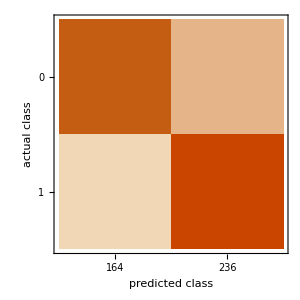

```mathematica
ClassifierMeasurements[c,testingData,"ConfusionMatrixPlot"]
```

```mathematica
ClassifierMeasurements[c,testingData,{"Precision","Recall","Accuracy"}]
```

{<|0→0.827778,1→0.931818|>,<|0→0.908537,1→0.868644|>,0.885}

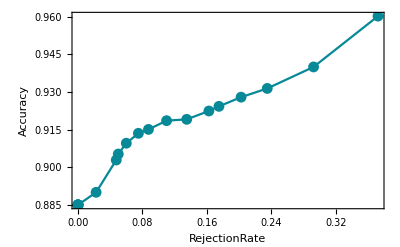

```mathematica
ClassifierMeasurements[c,testingData,"AccuracyRejectionPlot"]
```

#### Performance with Validation Dataset

One can see that the performance was not a flux.

```mathematica
ClassifierMeasurements[c,validationData,"Accuracy"]
```

0.911058

```mathematica
ClassifierMeasurements[c,validationData,{"Precision","Recall"}]
```

{<|0→0.866667,1→0.950226|>,<|0→0.938889,1→0.889831|>}

```mathematica
Insert[Grid[{{"Performance","Sentiment","Not Sentiment"},{"Precision",0.87,0.95},{"Recall",0.94,0.89}}],{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

Performance | Sentiment | Not Sentiment
Precision | 0.87 | 0.95
Recall | 0.94 | 0.89

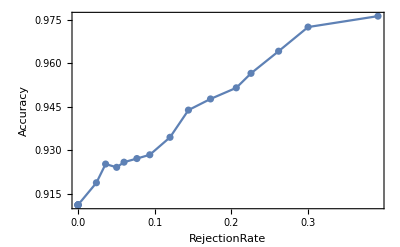

```mathematica
ClassifierMeasurements[c,validationData,"AccuracyRejectionPlot"]
```

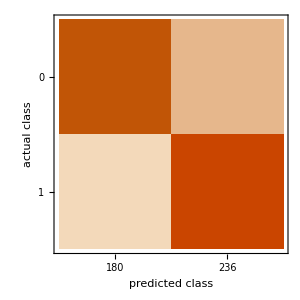

```mathematica
ClassifierMeasurements[c,validationData, "ConfusionMatrixPlot"]
```

```mathematica
DumpSave["c.mx",c]
```

{ClassifierFunction[…]}